## 3 | Quantum Linear Solvers

Solving linear systems is at the heart of countless applications, from physics simulations to machine learning. In quantum computing, the Quantum Linear Solver (QLS) is an approach designed to tackle the Quantum Linear Systems Problem (QLSP) efficiently.

## Harrow–Hassidim–Lloyd algorithm (HHL)

The main goal of HHL algorithm is too solve a linear system A.x=b by preparing a quantum state of the solution: HHL outputs x∝A^-1.b, enabling estimation of properties of x with (under sparsity, good conditioning, and oracle access) runtime polylogarithmic in the dimension.

### Theory

The Harrow–Hassidim–Lloyd (HHL) algorithm is a quantum procedure designed to solve systems of linear equations of the form:

A x⃗=b⃗

where A is a Hermitian matrix and b is a known vector. The importance of HHL lies in its potential to provide exponential speedup over classical algorithms under certain conditions, and in the fact that it serves as a foundation for several advanced algorithms in areas such as machine learning, optimization, and quantum simulation.

The quantum circuit implementing HHL (as shown in the schematic) is organized into five main sections:

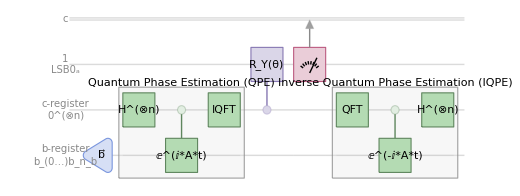

```mathematica
pe=QuantumCircuitOperator[{
QuantumOperator["RandomUnitary","Label"->"H^(⊗n)"]->{2},
"C"[QuantumOperator["RandomUnitary","Label"->"ⅇ^(ⅈ*A*t)"]]->{2,3},
QuantumOperator["RandomUnitary","Label"->"IQFT"]->{2}
}, "Label"->"Quantum Phase Estimation (QPE)"];
ipe=QuantumCircuitOperator[{
QuantumOperator["RandomUnitary","Label"->"QFT"]->{2},
"C"[QuantumOperator["RandomUnitary","Label"->"ⅇ^(-ⅈ*A*t)"]]->{2,3},
QuantumOperator["RandomUnitary","Label"->"H^(⊗n)"]->{2}
}, "Label"->"Inverse Quantum Phase Estimation (IQPE)"];
im=QuantumCircuitOperator[{
"I"->Range[2],
QuantumState["RandomPure","Label"->"b⃗"]->{3},
pe,
"C"[QuantumOperator["RY"[θ]]]->{2,1},
{1},
"I"->{2,3},
ipe
}];
im["Diagram",ImageSize->Full,
"WireLabels"->{"1\nLSB0_a","c-register\n0^(⊗n)","b-register\nb_(0…)b_n_b"},
"GateBackgroundStyle"->{
	"State\n Preparation"->LightOrange,
	"H^(⊗n)"|"ⅇ^(ⅈ*A*t)"|"ⅇ^(-ⅈ*A*t)"|"IQFT"|"QFT"->Lighter@Hue[0.33,0.3,0.79]
	},
"GateBoundaryStyle"->{
	"State\n Preparation"->Orange,
	"H^(⊗n)"|"ⅇ^(ⅈ*A*t)"|"ⅇ^(-ⅈ*A*t)"|"IQFT"|"QFT"->Darker@Hue[0.33,0.3,0.79]
	}
]
```

State b⃗ preparation

The vector b⃗ is encoded into the amplitudes of a register of qubits (the b-register). This step translates the classical problem into a quantum state b.

Quantum Phase Estimation (QPE)

QPE is applied to decompose b in the eigenbasis of A. The eigenvalues λ_i of A are encoded into an auxiliary register of clock qubits (the c-register).

Controlled Rotation & Measurement of the ancilla qubit

An auxiliary qubit (the ancilla, Least Significant Bit - LSB) is rotated in a way that depends on the eigenvalues stored in the c-register. This step effectively implements the action of A^-1, since the amplitudes are scaled by 1/λ_i . Measure the ancilla and keep only outcomes 1_a.

Inverse Quantum Phase Estimation (IQPE)

The inverse QPE is applied to disentangle the c-register from the b-register, ensuring that the solution is properly isolated in the latter.

Measurement

After post-selecting the ancilla in the desired state, the quantum system in the b-register encodes the solution x=A^-1 b. While the algorithm does not yield the classical solution vector directly, it enables the estimation of global properties of the solution, such as norms, probability distributions, or expectation values of observables.

This way, HHL combines three central tools of quantum computing:

superposition

phase estimation

controlled operations

And turn it into a coherent algorithm that addresses a fundamental problem in science and engineering.

### Introductory Approximate Implementation

#### Encoding Scheme

We implement the HHL algorithm for the following system of linear equations:

Piecewise[{{x_1-1/3 x_2=0
-1/3 x_1+x_2=1, or equivalently (1 | -1/3
-1/3 | 1)(x_1
x_2)=(0
1)}}]

with

A=(1 | -1/3
-1/3 | 1) , b⃗=(0
1)

```mathematica
A={{1,-1/3},{-1/3,1}};
b={0,1};
```

The eigenvalues and eigenvectors of 𝐴 are:

```mathematica
Eigensystem[A]
```

{{4/3,2/3},{{-1,1},{1,1}}}

```mathematica
{λ1,λ0}=Eigenvalues[A]
```

{4/3,2/3}

To encode the eigenvalues in the clock register, we use basis encoding. Two qubits are sufficient to represent the eigenvalues while maintaining their ratio:

(λ̃)_0=1 encoded as 01, (λ̃)_1=2 encoded as 10

This preserves the ratio λ_0/λ_1=0:

```mathematica
n=Divide@@Eigenvalues[A]
```

2

This gives a perfect encoding with 𝑛=2 (i.e., 𝑁=2^n=4). The evolution time 𝑡 is chosen to satisfy:

(λ̃)_j=Nλ_j t/2π

```mathematica
Solve[1==(2^n*λ0*t)/(2π),{t}]
```

{{t→(3 π)/4}}

```mathematica
Solve[2==(2^n*λ1*t)/(2π),{t}]
```

{{t→(3 π)/4}}

Since b⃗ is a 2-dimensional vector, it can be encoded using one qubit, so n_b=1

The exact solution to the linear system is:

```mathematica
LinearSolve[A,b]
```

{3/8,9/8}

We can verify the ratio of the squared amplitudes |x_1|^2∶|x_2|^2=1∶9:

```mathematica
Divide@@(Reverse[%]^2)
```

9

#### Implementation of the controlled-rotation of ancilla qubit

The next step is to rotate the ancilla qubit 0_a using a controlled RY(θ) rotation, where the control comes from the encoded eigenvalues in the clock (c-) register.

The rotation maps:

0_a -> √(1-C/OverTilde[λ_j]^2)0_a+C/((λ̃)_j)1_a

with θ=2ArcSin[C/((λ̃)_j)] and C is a constant chosen to maximize the probability of measuring 1_a.

The sum of the squares of the coefficients of 0 and 1 is 1, as required for a normalized quantum state. This also implies that C<=(λ̃)_j for all eigenvalues. Since the minimal (λ̃)_j=1 in our example, we set C=1 to maximize the probability of measuring 1_a during the ancilla measurement.

To implement this rotation in the algorithm,we solve for θ in terms of the encoded eigenvalues:

```mathematica
rotation=QuantumOperator["RY"[θ]]@QuantumState["0"];
rotation["Formula"]
```

Cos[θ/2]0+Sin[θ/2]1

```mathematica
θsolutions=Solve[rotation["AmplitudeList"]=={√(1-1/(λ̃)^2),1/(λ̃)},{θ}]/.ArcCos[x_]:>ArcSin[√(1-x^2)]//FullSimplify//Quiet
```

{{θ→-2 ArcSin[√(1/(λ̃)^2)]},{θ→2 ArcSin[√(1/(λ̃)^2)]}}

Assigning the actual eigenvalues:

```mathematica
θvalues=θ/.Last[θsolutions]/.λ̃->{1,2}
```

{π,π/3}

When the ancilla qubit is measured, it collapses to either 0_a or 1_a:

If it collapses to 0_a, the computation is discarded and repeated.

If it collapses to 1_a, the resulting state is proportional to the solution x, but the b-register is still entangled with the clock register.

To obtain the correct amplitudes in the computational basis, we need to uncompute the clock register. This disentangles the b-register from the clock qubits.

#### Quantum Phase Estimation

Quantum Phase Estimation (QPE) is a core eigenvalue estimation algorithm used in HHL. It consists of three main steps:

Creating a superposition of the clock qubits using Hadamard gates.

Applying controlled-unitary operations CU, where U=ⅇ^(ⅈ*A*t).

Performing the inverse quantum Fourier transform (IQFT) on the clock register.

The goal of QPE is to estimate the phase of the eigenvalues of the unitary operator U. In HHL, the controlled-𝑈 operation is applied to the b-register, conditioned on the clock qubits:

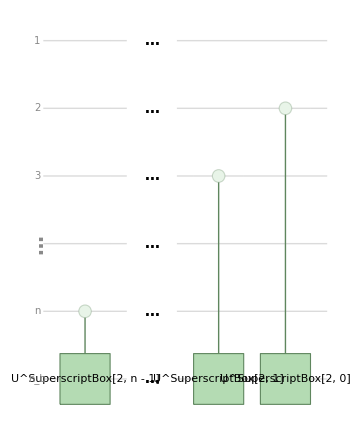

```mathematica
img=QuantumCircuitOperator[{
"I"->Range[4],
"C"[QuantumOperator["RandomUnitary","Label"->"U^SuperscriptBox[2, n - 1]"]]->{5,6},
Sequence@@Map[QuantumOperator["X","Label"->Style["…",15,Bold]]->{#}&,Range[6]],
"C"[QuantumOperator["RandomUnitary","Label"->"U^SuperscriptBox[2, 1]"]]->{3,6},
"C"[QuantumOperator["RandomUnitary","Label"->"U^SuperscriptBox[2, 0]"]]->{2,6}

}];
img["Diagram","WireLabels"->{1,2,3,Style[Rotate["…",π/2],20,Bold],"n","n_b"},"GateBackgroundStyle"->{
	Style["…",15,Bold]->None,
	"U^SuperscriptBox[2, n - 1]"|"U^SuperscriptBox[2, 1]"|"U^SuperscriptBox[2, 0]"->Lighter@Hue[0.33,0.3,0.79]
	},
"GateBoundaryStyle"->{
	Style["…",15,Bold]->None,
"U^SuperscriptBox[2, n - 1]"|"U^SuperscriptBox[2, 1]"|"U^SuperscriptBox[2, 0]"->Darker@Hue[0.33,0.3,0.79]
	}
]
```

For our 2×2 example (𝑛=2), the required operations are:

U^(2^1)=U^2 and U^(2^0)=U

To construct these gates, we first derive the unitary  U=ⅇ^(ⅈ*A*t) by performing a similarity transformation on A, exponentiating, and transforming back to the original basis:

```mathematica
U=QuantumOperator[MatrixExp[((3Pi)/4) I A]]
```

QuantumOperator[…]

Inspecting the resulting matrix:

```mathematica
U["Matrix"]//MatrixForm
```

(-1/2+ⅈ/2 | 1/2+ⅈ/2
1/2+ⅈ/2 | -1/2+ⅈ/2)

and for U^2:

```mathematica
(U^2)["Matrix"]//MatrixForm
```

(0 | -1
-1 | 0)

This gate encodes the Hamiltonian defined by the matrix A. Since U is unitary, its eigenvalues are roots of unity meaning that the phase of each eigenvalue of U is proportional to the corresponding eigenvalue of A. Consequently, when QPE is applied in HHL, the eigenvalues of A are encoded in the clock (c-) register through basis encoding, rather than storing their exact numerical values.

We can also implement QPE directly using the built-in “PhaseEstimation” gate in Wolfram Language:

```mathematica
QPE=QuantumCircuitOperator["PhaseEstimation"[U,n]][[2;;-3]]
```

QuantumCircuitOperator[…]

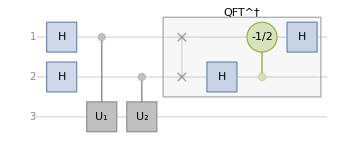

```mathematica
QPE["Diagram"]
```

Note that in our framework, the controlled-unitary gates are constructed in the opposite direction compared to this paper conventions. (remove this, focus only on our convention, we do not want to say we reproduce exactly a specific result etc)

#### Circuit Implementation

We can now implement the full HHL algorithm as a quantum circuit in Wolfram Language. The circuit includes the following steps:

Initialize the b-register with the state b.

Apply Quantum Phase Estimation (QPE) on the clock qubits.

Perform controlled RY(θ) rotations on the ancilla qubit, using the angles computed from the encoded eigenvalues.

Uncompute the QPE to disentangle the b-register from the clock qubits.

Measure the b-register to extract the solution.

```mathematica
HHL=QuantumCircuitOperator[{
QuantumState[b]->{4},"Barrier",
QPE->{2,3,4},"Barrier",
"C"["RY"[θvalues[[1]]]]->{2,1},
"C"["RY"[θvalues[[2]]]]->{3,1},
"Barrier",{1},"Barrier",
SuperDagger[QPE]->{2,3,4},
{4}
}]
```

QuantumCircuitOperator[…]

We can visualize the circuit:

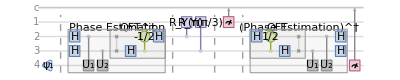

```mathematica
HHL["Diagram",Expand->2,ImageSize->Full]
```

Perform the measurement:

```mathematica
measurement=HHL[]
```

QuantumMeasurement[…]

After executing the circuit and measuring the qubits, the probabilities of each computational basis state are:

```mathematica
result=Normal[measurement["Probabilities"]]//FullSimplify
```

{00→3/16,01→3/16,10→1/16,11→9/16}

The solution correspond to the measured probabilities of the b-register. Selecting the relevant outcomes:

```mathematica
x=Values[result][[{3,4}]]
```

{1/16,9/16}

Finally, we verify that the ratio of the measured amplitudes matches the ratio of squared solutions obtained classically:

```mathematica
Divide@@x==Divide@@(LinearSolve[A,b]^2)
```

True

This confirms that the HHL implementation successfully encodes the solution to the linear system in the amplitudes of the b-register, consistent with the classical solution.

## Gray-Code Oracle HHL Algorithm

### Theory

Generate a random Hermitian matrix A∈ℂ^(n×n):

```mathematica
n=4;
a=QuantumOperator["RandomHermitian",n]["Matrix"]
HermitianMatrixQ[a]
```

SparseArray[…]

True

Generate a normalized random vector b∈ℂ^n:

```mathematica
b=RandomVariate[CircularUnitaryMatrixDistribution[2^n]][[All,1]];
Norm[b]
```

1.

Our main goal is to find x that satisfies A.x=b

Find the solution using classical linear solver and then normalize the result:

```mathematica
xClassical=LinearSolve[a,b]//Normalize
```

{-0.0310318+0.214092 ⅈ,-0.0814782+0.0908382 ⅈ,-0.20243+0.27246 ⅈ,-0.253612+0.292907 ⅈ,-0.152128+0.0721531 ⅈ,0.227304-0.223143 ⅈ,-0.29761-0.0905079 ⅈ,-0.0474046-0.0104791 ⅈ,-0.0721692+0.104622 ⅈ,-0.164166-0.332182 ⅈ,0.0292429+0.244291 ⅈ,0.316862+0.0640212 ⅈ,0.157334-0.0614232 ⅈ,0.17589-0.106518 ⅈ,0.187818-0.0698154 ⅈ,-0.119139+0.0204764 ⅈ}

Let’s find eigenvalues and eigenstates of A:

```mathematica
{λ,u}=Eigensystem[a];
u=Normalize/@u;
λ=Chop@λ;
```

We will not use them for HHL, but only for some sanity check. In other words, A is fed into HHL like a blackbox.

Choose t_0 such that the whole spectrum of A lies in the principle internal (-π/t_0,π/t_0]

```mathematica
t0=Floor@π/Norm[a]
(-π/t0<#<=π/t0)&/@λ//Apply[And]
```

1.50224

True

We shall take the Quantum-Phase-Estimation (QPE) unitary operator to be U=ⅇ^(ⅈ t_0 A)

```mathematica
U=QuantumOperator[MatrixExp[t0 I a]];
```

U=ⅇ^(ⅈ A t_0)=∑_j ⅇ^(ⅈ λ_j t_0)u_ju_j

```mathematica
U["Matrix"]-MatrixExp[ⅈ a t0]//Chop//Flatten//DeleteDuplicates
U["Matrix"]-Exp[ⅈ λ t0].(KroneckerProduct[#,Conjugate[#]]&/@u)//Chop//Flatten//DeleteDuplicates
```

{0}

{0}

Set the number of phase-estimation qubits:

```mathematica
m=6;
```

Create circuits with the initial state 0^(⊗m)b

```mathematica
stateprep=QuantumCircuitOperator[{QuantumState[b]}->m+Range[n]];
```

Create the Phase Estimation circuit for U given m:

```mathematica
qpe=QuantumCircuitOperator["PhaseEstimation"[U,m],Range[m+n]][[n+1;;-m-1]];
```

We have dropped some terms from the above circuit because our Phase Estimation circuit contains some NOT and measurement gates, too:

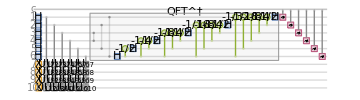

```mathematica
QuantumCircuitOperator["PhaseEstimation"[U,m],Range[m+n]]["Diagram"]
```

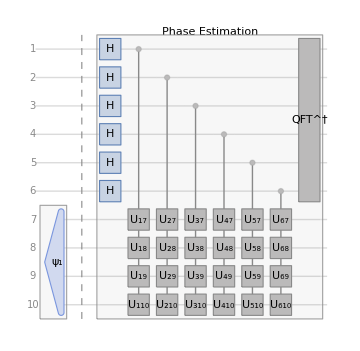

```mathematica
qc=QuantumCircuitOperator[{stateprep,"Barrier",qpe}];
qc["Diagram"]
```

Given eigenvalues, find the corresponding single phase-estimate register that holds the eigenvalue estimate (i.e., the nearest lattice to the eigenvalue y_j^*=Round[2^m(t_0 λ_j)/(2π)]):

```mathematica
yStar=Mod[Round[2^m t0/(2π)λ],2^m]
```

{33,34,29,28,26,39,39,24,45,18,17,51,53,8,60,1}

Given the initial state b, write it in terms of normalized eigenstates of U. It means b=∑_(j=0)^(2^n-1) β_j u_j

```mathematica
β=#.b&/@Conjugate[u];
```

The outcome of above circuit is  state qc 0^(⊗m)b=∑_(j=0)^(2^n-1) β_j∑_(y=0)^(2^m-1) 1/2^m(1-Exp[t_0 ⅈ 2^m(λ_j-y/2^m)])/(1-Exp[t_0 ⅈ (λ_j-y/2^m)])yu_j≃∑_(j=0)^(2^n-1) β_j y_j^*u_j

```mathematica
ψApproxQPE=β.MapThread[QuantumTensorProduct[QuantumState["Register"[m,#1]],QuantumState[#2]]&,{yStar,u}];
ψExactQPE=Sum[β[[k]]QuantumTensorProduct[Sum[1/2^m(1-Exp[ ⅈ 2π 2^m(λ[[k]] t0/(2π)-y/2^m)])/(1-Exp[ⅈ 2π(λ[[k]] t0/(2π)-y/2^m)])QuantumState["Register"[m,y]],{y,Range[0,2^m-1]}],QuantumState[u[[k]]]],{k,Range@Length[u]}];
```

Calculate the inner product of exact and approximated states vs the outcome of the quantum circuit:

```mathematica
Abs[ψApproxQPE["Dagger"][qc[]]["Scalar"]]^2
Abs[ψExactQPE["Dagger"][qc[]]["Scalar"]]^2
```

0.30817

1.

Centered unwrapping of the nearest lattice to the eigenvalue

OverTilde[y_j]=Piecewise[{{y_j^*, 0<=y_j^*<=2^(m-1)}, {y_j^*-2^m, 2^(m-1)<y_j^*<=2^m-1}}]:

```mathematica
yTilde=If[0<=#<=2^(m-1),#,#-2^m]&/@Range[0,2^m-1]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,-31,-30,-29,-28,-27,-26,-25,-24,-23,-22,-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1}

Note the binary representation of the centered unwrapping of the nearest lattice to the eigenvalue is the same as the normal one (after some Mod 2^m):

```mathematica
IntegerDigits[Mod[yTilde,2^m],2,m]==IntegerDigits[Range[0,2^m-1],2,m]
```

True

Given the centered unwrapping of the nearest lattice, compute the eigenvalue proxy (λ̃)_y=(2π)/t_0(ỹ)/2^m:

```mathematica
λTilde=(2π)/t0 yTilde/2^m
```

{0.,0.0653522,0.130704,0.196057,0.261409,0.326761,0.392113,0.457465,0.522817,0.58817,0.653522,0.718874,0.784226,0.849578,0.91493,0.980283,1.04563,1.11099,1.17634,1.24169,1.30704,1.3724,1.43775,1.5031,1.56845,1.6338,1.69916,1.76451,1.82986,1.89521,1.96057,2.02592,2.09127,-2.02592,-1.96057,-1.89521,-1.82986,-1.76451,-1.69916,-1.6338,-1.56845,-1.5031,-1.43775,-1.3724,-1.30704,-1.24169,-1.17634,-1.11099,-1.04563,-0.980283,-0.91493,-0.849578,-0.784226,-0.718874,-0.653522,-0.58817,-0.522817,-0.457465,-0.392113,-0.326761,-0.261409,-0.196057,-0.130704,-0.0653522}

Double-check that -π/t_0<(λ̃)_y<=π/t_0

```mathematica
-π/t0<#<=π/t0&/@λTilde//Apply[And]
```

True

Choose a fixed inversion scale 0<γ<=|(λ̃)_y|_min

```mathematica
γ=Min[DeleteCases[Abs[λTilde],0.|0]]
```

0.0653522

Given the inversion scale, compute the eigenvalue-inversion rotation (if (λ̃)_y=0, no rotation):

θ_j=2 ArcSin[γ/(λ̃)_j]

```mathematica
θλ=If[#==0||#==0.,0.,2ArcSin[γ/#]]&/@λTilde
```

{0.,3.14159,1.0472,0.679674,0.505361,0.402716,0.334896,0.286695,0.250656,0.222682,0.200335,0.18207,0.16686,0.153998,0.142979,0.133432,0.125082,0.117715,0.111168,0.105312,0.100042,0.0952741,0.0909404,0.0869839,0.0833575,0.0800213,0.0769421,0.074091,0.0714438,0.0689792,0.066679,0.0645273,0.0625102,-0.0645273,-0.066679,-0.0689792,-0.0714438,-0.074091,-0.0769421,-0.0800213,-0.0833575,-0.0869839,-0.0909404,-0.0952741,-0.100042,-0.105312,-0.111168,-0.117715,-0.125082,-0.133432,-0.142979,-0.153998,-0.16686,-0.18207,-0.200335,-0.222682,-0.250656,-0.286695,-0.334896,-0.402716,-0.505361,-0.679674,-1.0472,-3.14159}

Check the rotation effect R_Y(θ_j)0=√(1-(γ/((λ̃)_j))^2)0+Abs[γ/((λ̃)_j)]1

```mathematica
Table[QuantumOperator["RY"[θλ[[j]]]][]["StateVector"]-If[λTilde[[j]]==0.||λTilde[[j]]==0,{1,0},{√(1-(γ/λTilde[[j]])^2),γ/λTilde[[j]]}]//Chop,{j,Length@λTilde}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

One can find the binary representation of (ỹ)_j in m-qubit. We will interpret each binary result as condition qubits (0 or 1):

```mathematica
AssociationMap[IntegerDigits[Mod[#,2^m],2,m]&,yTilde]
```

<|0→{0,0,0,0,0,0},1→{0,0,0,0,0,1},2→{0,0,0,0,1,0},3→{0,0,0,0,1,1},4→{0,0,0,1,0,0},5→{0,0,0,1,0,1},6→{0,0,0,1,1,0},7→{0,0,0,1,1,1},8→{0,0,1,0,0,0},9→{0,0,1,0,0,1},10→{0,0,1,0,1,0},11→{0,0,1,0,1,1},12→{0,0,1,1,0,0},13→{0,0,1,1,0,1},14→{0,0,1,1,1,0},15→{0,0,1,1,1,1},16→{0,1,0,0,0,0},17→{0,1,0,0,0,1},18→{0,1,0,0,1,0},19→{0,1,0,0,1,1},20→{0,1,0,1,0,0},21→{0,1,0,1,0,1},22→{0,1,0,1,1,0},23→{0,1,0,1,1,1},24→{0,1,1,0,0,0},25→{0,1,1,0,0,1},26→{0,1,1,0,1,0},27→{0,1,1,0,1,1},28→{0,1,1,1,0,0},29→{0,1,1,1,0,1},30→{0,1,1,1,1,0},31→{0,1,1,1,1,1},32→{1,0,0,0,0,0},-31→{1,0,0,0,0,1},-30→{1,0,0,0,1,0},-29→{1,0,0,0,1,1},-28→{1,0,0,1,0,0},-27→{1,0,0,1,0,1},-26→{1,0,0,1,1,0},-25→{1,0,0,1,1,1},-24→{1,0,1,0,0,0},-23→{1,0,1,0,0,1},-22→{1,0,1,0,1,0},-21→{1,0,1,0,1,1},-20→{1,0,1,1,0,0},-19→{1,0,1,1,0,1},-18→{1,0,1,1,1,0},-17→{1,0,1,1,1,1},-16→{1,1,0,0,0,0},-15→{1,1,0,0,0,1},-14→{1,1,0,0,1,0},-13→{1,1,0,0,1,1},-12→{1,1,0,1,0,0},-11→{1,1,0,1,0,1},-10→{1,1,0,1,1,0},-9→{1,1,0,1,1,1},-8→{1,1,1,0,0,0},-7→{1,1,1,0,0,1},-6→{1,1,1,0,1,0},-5→{1,1,1,0,1,1},-4→{1,1,1,1,0,0},-3→{1,1,1,1,0,1},-2→{1,1,1,1,1,0},-1→{1,1,1,1,1,1}|>

Create the corresponding eigenvalue-inversion circuit which is a collection of mutiplexers:

```mathematica
inv=QuantumCircuitOperator[MapThread["C"["RY"[#2],Sequence@@(#1+1)]&,{Lookup[{1,0}][PositionIndex[IntegerDigits[Mod[#,2^m],2,m]]]&/@yTilde/._Missing:>{},θλ}]];
inv["Diagram","ShowGateLabels"->False]
```

One can show that given the angles, the eigenvalue-inversion can be written as Gray-code circuit (which contains only 1 and 2 qubit gates):

```mathematica
gray=QuantumCircuitOperator["GrayOracle"[θλ,m,1]];
gray["Diagram","ShowGateLabels"->False]
```

Check the multiplexers and rotations are the same as Gray-code circuit:

```mathematica
gray["Matrix"]-inv["Matrix"]//Normal//Chop//Flatten//DeleteDuplicates
```

{0}

Put everything together and create the corresponding HHL circuit (note in post-selection 10^(⊗m) at the end):

```mathematica
hhl=(qc["Shift"]/*inv/*qpe["Shift"]["Dagger"]/*QuantumOperator[QuantumTensorProduct[QuantumState["1"],QuantumState["Register"[m]]]["Dagger"]]);
hhl["Flatten"]["Diagram","ShowGateLabels"->False]
```

Get the normalized final state of HHL circuit:

```mathematica
finalState=hhl[]["Normalize"]
```

QuantumState[…]

Find its amplitudes:

```mathematica
xHHL=finalState["AmplitudesList"]
```

{-0.0262314+0.209516 ⅈ,-0.0858042+0.0949136 ⅈ,-0.206077+0.273703 ⅈ,-0.253523+0.288911 ⅈ,-0.158096+0.0704409 ⅈ,0.230689-0.216771 ⅈ,-0.291949-0.0806227 ⅈ,-0.0509824-0.011092 ⅈ,-0.0749805+0.103225 ⅈ,-0.165223-0.33248 ⅈ,0.0247272+0.244743 ⅈ,0.324887+0.0606934 ⅈ,0.151716-0.058671 ⅈ,0.178508-0.110225 ⅈ,0.183518-0.0681284 ⅈ,-0.125961+0.0278092 ⅈ}

Compare the result with the one from the classical linear solver:

```mathematica
Abs[Conjugate[xHHL].xClassical]^2
```

0.999368

### Implementation

Generate HHL circuit that takes  A,  b, and number of ancillary qubits:

```mathematica
ClearAll[HHL]
HHL[A_?SquareMatrixQ,b_?VectorQ,prec:_Integer?Positive:4]:=
Block[{d,qpe,t0,yTilde,λTilde,θλ,γ},
d=Log2@Length[b];
t0=Floor@π/Norm[A];
yTilde=If[0<=#<=2^(prec-1),#,#-2^prec]&/@Range[0,2^prec-1];
λTilde=(2π)/t0 yTilde/2^prec;
γ=Min[DeleteCases[Abs[λTilde],0.|0]];
θλ=If[#==0||#==0.,0.,2ArcSin[γ/#]]&/@λTilde;
QuantumCircuitOperator[{
QuantumState[Normalize[b]]->1+prec+Range[d],
"Barrier",
qpe=QuantumCircuitOperator["PhaseEstimation"[QuantumOperator[MatrixExp[t0 I A]],prec],1+Range[prec+d]][[d+1;;-prec-1]],
"Barrier",
QuantumCircuitOperator["GrayOracle"[θλ,prec,1],"Eigenvalue Inversion"],
"Barrier",
qpe["Dagger"],
"Barrier",
QuantumOperator[QuantumState["1"<>StringJoin[ConstantArray["0",prec]]]["Dagger"]]
}
]/;IntegerQ[d]
]
```

Generate a complex-valued random Hermitian of n-qubits (a matrix of n×n)

```mathematica
n=4;
a=QuantumOperator["RandomHermitian",n]["Matrix"];
HermitianMatrixQ[a]
```

True

Generate a complex-valued random vector b:

```mathematica
b=QuantumOperator["RandomUnitary",n]["Matrix"][[All,1]];
Norm[b]
```

1.

Create HHL circuit:

```mathematica
hhl=N@HHL[a,b,6];
hhl["Diagram","ShowGateLabels"->False]
```

Given the result of above circuit, find corresponding amplitudes, and then normalize them to get solution of HHL solver:

```mathematica
xHHL=hhl[]["Normalize"]["AmplitudesList"]//Chop
```

{-0.0624492-0.194449 ⅈ,-0.211638-0.181538 ⅈ,0.127707-0.168527 ⅈ,0.203789-0.12266 ⅈ,0.273516-0.328501 ⅈ,0.0803508+0.0250782 ⅈ,-0.0170633+0.0739222 ⅈ,-0.23632+0.157087 ⅈ,-0.289865-0.112049 ⅈ,-0.0637741+0.101259 ⅈ,-0.270351+0.0528152 ⅈ,-0.248793-0.0200643 ⅈ,0.100543+0.0477517 ⅈ,0.024687+0.329258 ⅈ,0.338678+0.0936353 ⅈ,0.0937434+0.0205797 ⅈ}

Find the corresponding solution using classical approach:

```mathematica
xClassical=Normalize@LinearSolve[a,b]
```

{-0.0592154-0.191945 ⅈ,-0.212795-0.182558 ⅈ,0.120002-0.169802 ⅈ,0.209812-0.123074 ⅈ,0.274832-0.324801 ⅈ,0.0778722+0.0235326 ⅈ,-0.017339+0.073759 ⅈ,-0.23697+0.152727 ⅈ,-0.291812-0.107079 ⅈ,-0.0634163+0.104476 ⅈ,-0.272168+0.0582107 ⅈ,-0.246798-0.0213585 ⅈ,0.0996423+0.0445446 ⅈ,0.0196041+0.328481 ⅈ,0.341778+0.0936149 ⅈ,0.0965507+0.0170846 ⅈ}

Compare classical result with the quantum one (using the inner product as a measure; the closer to one the better)"

```mathematica
Abs[Conjugate[xClassical].xHHL]^2
```

0.999696

As mentioned, the number of phase-estimation qubits (3rd argument) determines the precision of final outcome. Execute HHL with less phase-estimation qubits::

```mathematica
xHHLLowPrecision=N[HHL[a,b,5]][]["Normalize"]["AmplitudesList"]//Chop
```

{-0.000648279-0.130177 ⅈ,-0.22391-0.193131 ⅈ,-0.0255832-0.20001 ⅈ,0.325005-0.115689 ⅈ,0.276105-0.237296 ⅈ,0.0446894+0.00503929 ⅈ,-0.0226627+0.046376 ⅈ,-0.236123+0.0663068 ⅈ,-0.303376-0.00909108 ⅈ,-0.0571509+0.156154 ⅈ,-0.289543+0.153207 ⅈ,-0.200192-0.0633506 ⅈ,0.0751016-0.0182279 ⅈ,-0.0745249+0.298917 ⅈ,0.377542+0.0730971 ⅈ,0.123252-0.0587272 ⅈ}

Quantify the good ness of HHL result in compared with the classical result:

```mathematica
Abs[Conjugate[xClassical].xHHLLowPrecision]^2
```

0.894533

The precision of HHL (how good it performs) can be understood in terms of nearest lattice to the eigenvalue, i.e., the finesse of the lattice grid. The coefficients of the terms in the exact formula of the state after QPE has a Dirichlet-kernel form |1/2^m(1-Exp[t_0 ⅈ 2^m(λ_j-y/2^m)])/(1-Exp[t_0 ⅈ (λ_j-y/2^m)])|^2=1/2^(2m)|Sin[π (2^m λ t_0/(2π) -y)]/Sin[π (λ t_0/(2π) -y)]|^2. If they are localized around an eigenvalue, it means the lattice grid is good, otherwise not.

Final comment: we put the initial b state directly into our HHL circuit. We also have state-preparation circuit, meaning one can generate the state using some gates

```mathematica
prep=QuantumCircuitOperator["StatePreparation"[QuantumState[b]]];
prep["Diagram","ShowGateLabels"->False]
```

-Graphics-

```mathematica
prep[]==QuantumState[b]
```

True

## Variational Quantum Linear Solver (VQLS)

### Theory

The Variational Quantum Linear Solver (VQLS) is a a hybrid quantum-classical technique designed to address Quantum Linear Systems Problem (QLSP). It aims to find linear system solutions using quantum computing techniques. The corresponding quantum algorithm can be summarized as follows:

Given:

A quantum state b such that b=U0

2^n x 2^n dimensional matrix A such that A=(∑_0)^(L-1)c_l A_l where c_l ϵ  ℂ and A_lare unitary gates

One wants to prepare:

A quantum state x  such that ψ=Ax  and ψ/(√ψψ)->b

#### VQLS Approach

We will get an approximate x  state using a variational quantum circuit V(ω), in other words:

x,=V(ω)0

Then, we look to optimize the parameters ω={ω_0,ω_1,... } in order to minimize the cost function. We can propose the following cost function:

C_G=1/ψψ x H_G x
=1/ψψ A^†(𝟙-bb)A=1/ψψ Tr[ψψ(𝟙-bb)]
=1- |bψ|,^2

where ψ=ψ/(√ψψ).

You can write C_G explicitly as:

C_G=1- (∑_(l,l') c_l c_l'^*0 V^†A_l'^†U00 U^†A_l V0)/(∑_(l,l') c_l c_l'^*0 V^†A_l'^†A_l V0)

As  Bravo-Prieto explains, a barren plateau might arise from using this global cost function. In other words, it indicates that the gradients of the cost function with respect to the parameters of the quantum circuit vanish exponentially as the number of qubits n increases. When gradients become extremely small, it becomes hard for optimization algorithms to make meaningful progress in adjusting the parameters of the quantum circuit to minimize the cost function.

Instead, we can work with a “local” version of it and apply the Hadamard test to estimate the expectation values. According to Bravo-Prieto, the local version is calculaton by changing H_G->H_L=[A^†U(𝟙-1/n∑ 0_j 0_j⊗𝟙_(j^-))U^†A],, where j is the qubit index and 𝟙_(j^-) the indentity on all qubits except j.

Finally we can express the local cost function explicitly as:

C_L=1/2-1/(2n)∑_(j=0)^(n-1) (∑_(l,l') c_l c_l'^*0 V^†A_l'^†U,,, Z_j U^†A_l V0)/(∑_(l,l') c_l c_l'^*0 V^†A_l'^†A_l V0)
=1/2-1/(2n)∑_(j=0)^(n-1) (∑_(l, l') c_l c_l'^*μ_(l , l', j))/(∑_(l,l') c_l c_l'^*μ_(l , l', -1))

where μ_(l , l',j)= 0 V^†A_l'^†U Z_J U^†A_l V0 , Z_-1->𝟙 and  C_G->0 <->C_L->0.

References used for this section:

Bravo-Prieto, C., LaRose, R., Cerezo, M., Subasi, Y., Cincio, L., & Coles, P. J. (2019). Variational Quantum Linear Solver. arXiv. https://doi.org/10.48550/ARXIV.1909.05820

Mari, A. Variational Quantum Linear Solver. PennyLane Demos. https://pennylane.ai/qml/demos/tutorial_vqls/

### QLSP introductory example

In this implementation we will consider the first qubit as our auxiliary qubit, since in the Wolfram QuantumFramework negative qubits and qubit 0 are used only for classical bits.

For this example we will consider a 2 qubits system plus an auxiliary qubit.

A=X_2 H_3

b=U0=H_2 H_3 0

where the operator’s index indicate the qubit it is applied on.

Given the ansatz:

x=V(ω)0=[R_y(ω_2)⊗R_y(ω_3)]H_2 H_3 0

We will proceed to build the circuit to minimize C_L.

#### Circuit Implementation

First we define the gates associated with the example:

The unitary matrix such that b=U_b 0 :

```mathematica
Ub=QuantumCircuitOperator[{"H"->{2},"H"->{3}},"Label"->"U_b"];
```

Because our goal is to conduct a Hadamard test, it’s necessary for the unitary operation A to be controlled  by the state of an auxiliary qubit:

```mathematica
ControlledAGate=QuantumCircuitOperator[{"CNOT"->{1,2},"CH"->{1,3}},"Label"->"A_2"];
```

Next, we implement the variational quantum circuit that generates a guess for x:

x=V(ω)0=[R_x(ω_1)⊗R_x(ω_2)]H_2 H_3 0

The first layer prepare an equal superposition of states and the second layer is the ansatz proposed before:

```mathematica
VariationalBlock=QuantumCircuitOperator[
{"H"->{1,2},
"RY"[ω1]->{1},"RY"[ω2]->{2}},
"Label"->"V(ω)","Parameters"->{ω1,ω2}];
```

In order to obtain μ_(l , l', j) we will implement a circuit that will deploy a Hadamard test:

1. We first apply a Hadamard in the auxiliar qubit to prepare a state in superposition.

2. We apply a Phase Shift to estimate the imaginary or real part of the μ: Re[μ] when θ → 0 and Im[μ] when θ → -π/2.

3. Apply the Variational Circuit to generare a guess on x.

4. Apply the Controlled Gate corresponding to the A_lcomponent.

5. Apply the adjoint U_b, but in this case is the same as U_b.

6. Implement a controlled Z operator from the auxiliar qubit to the system qubit j. For the normalization calculation, we will use j = -1 to apply the identity.

7. From this step, we will “undo” our operations, first by applying U_b.

8. Apply the A_l Controlled gate‘s adjoint, which is the same as A_l.

9. Last Hadamard gate for the Hadamard test

At the end we apply a QuantumMeasureOperator to measure the expectation values.

```mathematica
Clear[LocalHadamardCircuit];
LocalHadamardCircuit[j_]:=QuantumCircuitOperator[{
"Hadamard"->{1},
"P"[θ],
VariationalBlock->{2,3},
ControlledAGate,
Ub,
If[!MatchQ[j,-1],"CZ"->{1,j},Nothing],
Ub,
ControlledAGate,
"Hadamard"->{1},
QuantumMeasurementOperator["Z"->{-1,1},{1}]
},
"Parameters"->{ω1,ω2,θ}
]
```

You can test the multiple variations of the circuit for each controlled gate:

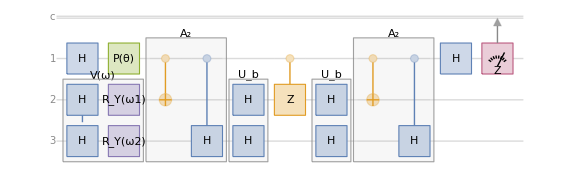

```mathematica
LocalHadamardCircuit[2]["Diagram",ImageSize->Large]
```

#### Optimized Circuit Implementation

As you might notice, the past implementation might be slow if we want to obtain the expected value for each combination. Moreover, the local cost function that we will implement later to optimize will need to calculate the mean value multiple times.

Instead we could try to use the useful KroneckerProduct to build the same circuit with all the variations.

We can re-implement CZ gate, since it depends in which qubit it will be applied on:

```mathematica
ControlledGateZ=QuantumOperator[
QuantumOperator["CZ"->{1,2}]*KroneckerDelta[j,2]+QuantumOperator["CZ"->{1,3}]*KroneckerDelta[j,3]+QuantumOperator["I"]*KroneckerDelta[j,-1],
"Label"->"Controlled Z_j Gate"
];
```

As you might notice, we just apply a KroneckerDelta to get rid of the qubits we won’t be using for each case, this is possible since we already know how many qubits we are working on.

As the previous subsection, we implement the Hadamard test:

```mathematica
ClearAll[LocalHadamardCircuit];
LocalHadamardCircuit=QuantumCircuitOperator[{
"Hadamard"->{1},
"P"[θ],
VariationalBlock->{2,3},
ControlledAGate,
Ub,
ControlledGateZ,
Ub,
ControlledAGate,
"Hadamard"->{1}
},"Parameters"->{ω1,ω2,j,θ}];
```

Check out the newly implemented circuit diagram:

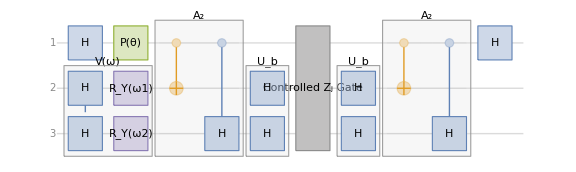

```mathematica
LocalHadamardCircuit["Diagram",ImageSize->Large]
```

#### Local Cost Function

You might noticed that we didn’t include the QuantumMeasurementOperator. In order to calculate even faster the mean values, we will calculate ϕHϕ where H=σ_z ⊗𝟙 ⊗𝟙:

```mathematica
ket=Normal[LocalHadamardCircuit[]["StateVector"]];
```

```mathematica
bra=ConjugateTranspose[ket];
```

Finally we use the ket and bra obtained to calculate the expected value:

```mathematica
H=Normal[QuantumOperator[{"Z"->{1},"I"->{2,3}}]["Matrix"]];
```

```mathematica
LocalMean=bra.H.ket;
```

We just obtained the Symbolic Mean value of our circuit, in order to replace the variables quickly we define the following function:

```mathematica
ClearAll[LocalMeanValues];
LocalMeanValues[ω1_,ω2_,j_,θ_]=LocalMean;
```

Now we will implement all the functions needed for the cost function defined in the Theory section:

Define  μ_(l,v,j) , note that you get Re[μ] when θ → 0 and Im[μ] when θ → -π/2:

```mathematica
ClearAll[μ]
μ[ω1_,ω2_,j_]:=Module[{μRe,μIm},

μRe=LocalMeanValues[ω1,ω2,j,0];
μIm=LocalMeanValues[ω1,ω2,j,-π/2.];


N[μRe + j  μIm]
]
```

Next, implement the normalization term:

```mathematica
ClearAll[PsiNorm];
PsiNorm[ω1_,ω2_]:=Abs[μ[ω1,ω2,-1]];
```

Following the C_L equation, we define the cost function:

```mathematica
ClearAll[LocalCost];
LocalCost[ω1_,ω2_]:=0.5-(0.5/(3PsiNorm[ω1,ω2]))Abs[μ[ω1,ω2,2]+μ[ω1,ω2,3]]
```

#### Symbolic Cost Function Optimization

Let’s calculate the symbolic equation for the cost function. It is not that huge of an expression, but surely not visually pleasant to show here:

```mathematica
ClearAll[LocalCostFunction];
LocalCostFunction[ω1_,ω2_]=Simplify[LocalCost[ω1,ω2],{ω1,ω2}∈ Reals];//AbsoluteTiming
```

{8.71263,Null}

Since we have the symbolic function, we can use NMinize:

```mathematica
GradientParameters=NMinimize[LocalCostFunction[ω1,ω2],{ω1,ω2}]
```

{0.166667,{ω1→-9.87416×10^-11,ω2→-1.5708}}

#### Numerical Cost Function Optimization

We can use our previously defined LocalCost for numerical calculations using a numerical gradient descent:

```mathematica
ω= 0.001 *RandomVariate[NormalDistribution[],2];
```

```mathematica
NGradientParameters=GradientDescent[LocalCost,ω,"LearningRate"->0.8,"MaxIterations"->15];//AbsoluteTiming
```

{20.2959,Null}

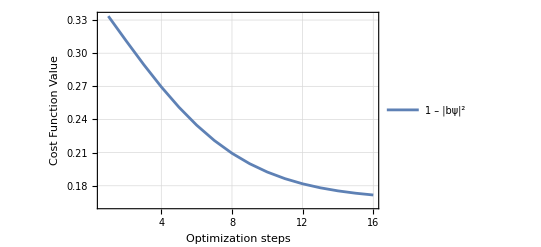

```mathematica
ListPlot[LocalCostFunction@@@NGradientParameters,Joined->True,GridLines->Automatic,PlotRange->All,Frame->True,FrameLabel->{"Optimization steps","Cost Function Value"},PlotLegends->{"1 – |bψ|^2"}]
```

#### Classical Linear System Solving

We can build the A matrix and statebof the present problem:

A=X_2 H_3

b=U0=H_2 H_3 0

Solve the system by operating over the correspondant matrices:

```mathematica
A=KroneckerProduct[PauliMatrix[1],HadamardMatrix[2]];
b=ConstantArray[1/Sqrt[8],4];
{"A"->MatrixForm[A],"b"->MatrixForm[b]}
```

{A→(0 | 0 | 1/(√2) | 1/(√2)
0 | 0 | 1/(√2) | -1/(√2)
1/(√2) | 1/(√2) | 0 | 0
1/(√2) | -1/(√2) | 0 | 0),b→(1/(2 √2)
1/(2 √2)
1/(2 √2)
1/(2 √2))}

Finally, compute the probabilities:

```mathematica
LinearSystemResult=Normalize[LinearSolve[A,b]]^2;
Thread[Delete[0]@#&/@Tuples[{"0","1"},2]->LinearSystemResult]
```

{0,0→1/2,0,1→0,1,0→1/2,1,1→0}

#### Symbolic & Numeric Quantum Circuit Result

Test the Variational circuit with the optimized parameters results:

```mathematica
VariationalMeasurement=QuantumCircuitOperator[{VariationalBlock,{1},{2}}][];
```

The symbolic optimization resultant probabilities:

```mathematica
SymbolicResult=VariationalMeasurement[Association[GradientParameters[[2]]]]["Probabilities"]
```

<|00→0.5,01→1.61337×10^-17,10→0.5,11→1.61337×10^-17|>

The numerical optimization resultant probabilities:

```mathematica
NumericalResult=VariationalMeasurement[AssociationThread[{ω1,ω2},Last@NGradientParameters]]["Probabilities"]
```

<|00→0.492425,01→0.007484,10→0.492604,11→0.00748671|>

We can calculate how different one distribution is from another using a Kolmogorov Smirnov Test:

```mathematica
KolmogorovSmirnovTest[Values@SymbolicResult,LinearSystemResult]
```

0.657143

```mathematica
KolmogorovSmirnovTest[Values@NumericalResult,LinearSystemResult]
```

0.771429

In this case, the number is considered big enough to indicate that the results are from the reference distribution.

Let’s plot the probabilities for a visual comparison:

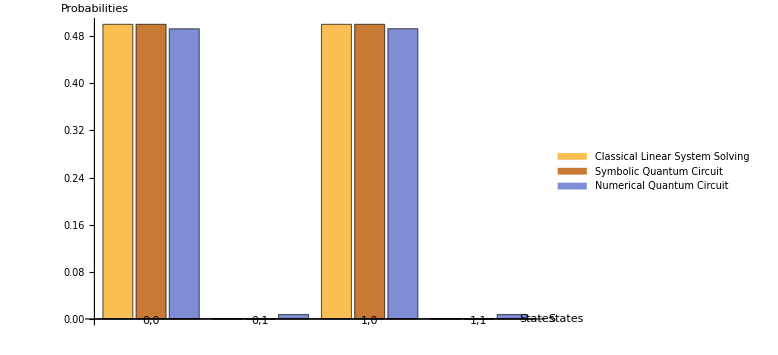

```mathematica
BarChart[Transpose[{LinearSystemResult,Values@SymbolicResult,Values@NumericalResult}],ChartLayout->"Grouped",ChartLabels->{Delete[0]@#&/@Tuples[{"0","1"},2],None},ChartLegends->{"Classical Linear System Solving","Symbolic Quantum Circuit","Numerical Quantum Circuit"},ImageSize->Large,AxesLabel->{"States","Probabilities"}]
```

### QLSP implemented in Rigetti Quantum Computer

This QLSP was already tested by Bravo-Prieto using Rigetti’s quantum chip 16Q Aspen-4.

For this example we will consider a 3 qubits system plus an auxiliar qubit.

A=c_2 A_2+c_3 A_3+c_4 A_4=𝟙+0.2 X_2 Z_3+0.2 X_2

b=U0=H_2 H_3 H_4 0

where the operator’s index indicate the qubit it is applied on.

Given the ansatz:

x=V(ω)0=[R_y(ω_2)⊗R_y(ω_3)⊗R_y(ω_4)]H_2 H_3 H_4 0

We will proceed to build the circuit to minimize C_L.

#### Circuit Implementation

As the previous QLSP,  we define the gates associated with the example:

The unitary matrix such that b=U_b 0 :

```mathematica
Ub=QuantumCircuitOperator[{"H"->{2,3,4}},"Label"->"U_b"];
```

In this case we have multiple controlled A_l  gates to perform the Hardamard–test and controlled Z_j gates as the previous example, so we will directly implement an optimized version of the circuit using KroneckerProduct:

```mathematica
ControlledGateA=QuantumOperator[QuantumOperator["I"]*KroneckerDelta[l,2]+QuantumOperator[{"CNOT"->{1,2},"CZ"->{1,3}}]*KroneckerDelta[l,3]+QuantumOperator[{"CNOT"->{1,2}}]*KroneckerDelta[l,4],
"Parameters"->{l},
"Label"->"Controlled A_l Gate"];
```

```mathematica
ControlledGateZ=QuantumOperator[
QuantumOperator["CZ"->{1,2}]*KroneckerDelta[j,2]+QuantumOperator["CZ"->{1,3}]*KroneckerDelta[j,3]+QuantumOperator["CZ"->{1,4}]*KroneckerDelta[j,4]+QuantumOperator["I"]*KroneckerDelta[j,-1],
"Parameters"->{j},
"Label"->"Controlled Z_j Gate"
];
```

Next, we implement the variational quantum circuit that generates a guess for x:

x=V(ω)0=[R_y(ω_1)⊗R_y(ω_2)⊗R_y(ω_3)]H_2 H_3 H_4 0

```mathematica
VariationalBlock=QuantumCircuitOperator[{
"Hadamard"->{1,2,3},
"RY"[ω1]->{1},"RY"[ω2]->{2},"RY"[ω3]->{3}
},
"Label"->"V(ω)",
"Parameters"->{ω1,ω2,ω3}];
```

In order to obtain μ_(l , l', j) we will implement a circuit that will deploy a Hadamard test:

```mathematica
ClearAll[LocalHadamardCircuit];
LocalHadamardCircuit=QuantumCircuitOperator[{
"Hadamard"->{1},
"P"[θ],
VariationalBlock->{2,3,4},
ControlledGateA,
Ub,
ControlledGateZ,
Ub,
ControlledGateA[<|l->lp|>],
"Hadamard"->{1}
},"Parameters"->{ω1,ω2,ω3,l,lp,j,θ}];
```

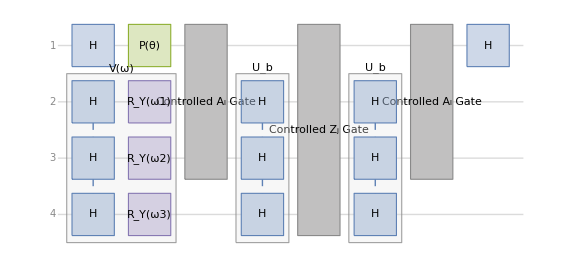

```mathematica
LocalHadamardCircuit["Diagram",ImageSize->Large]
```

#### Local Cost Function

Now let’s calculate the symbolic mean value:

```mathematica
ket=Normal[LocalHadamardCircuit[]["StateVector"]];
```

```mathematica
bra=ConjugateTranspose[ket];
```

Finally we use the ket and bra obtained to calculate the expected value:

```mathematica
H=Normal[QuantumOperator[{"Z"->{1},"I"->{2,3,4}}]["Matrix"]];
```

```mathematica
LocalMean=bra.H.ket;
```

Now we redefine the functions, since we are dealing with more ω_i variables from our Variational Circuit:

```mathematica
ClearAll[LocalMeanValues];
LocalMeanValues[ω1_,ω2_,ω3_,l_,lp_,j_,θ_]=LocalMean;
```

Now we will implement all the functions needed for the cost function defined in the Theory section:

Define  μ_(l,v,j) :

```mathematica
ClearAll[μ]
μ[ω1_,ω2_,ω3_,l_,lp_,j_]:=Module[{μRe,μIm},

μRe=LocalMeanValues[ω1,ω2,ω3,l,lp,j,0];
μIm=LocalMeanValues[ω1,ω2,ω3,l,lp,j,-π/2.];


N[μRe + j  μIm]
]
```

We prepend a 0 value in the constants from the A problem matrixso it later matches with the system qubits index:

```mathematica
c={0.,1.0,0.2,0.2};
```

Now we will implement the normalization term. In this case l and lp values correspond to our system qubits:

```mathematica
ClearAll[PsiNorm];
PsiNorm[ω1_,ω2_,ω3_]:=Abs[Sum[c[[l]]*Conjugate[c[[lp]]]*μ[ω1,ω2,ω3,l,lp,-1],{l,{2,3,4}},{lp,{2,3,4}}]];
```

Following the C_L equation, we define the cost function:

```mathematica
ClearAll[LocalCost];
LocalCost[ω1_,ω2_,ω3_]:=0.5-(0.5/(3PsiNorm[ω1,ω2,ω3]))Abs[Sum[c[[l]]*Conjugate[c[[lp]]]*μ[ω1,ω2,ω3,l,lp,j],
{l,{2,3,4}},{lp,{2,3,4}},{j,{2,3,4}}]]
```

#### Symbolic Cost Function Optimization

Let’s calculate the symbolic equation for the cost function. It is not that huge of an expression, but surely not visually pleasant to show here:

```mathematica
ClearAll[LocalCostFunction];
LocalCostFunction[ω1_,ω2_,ω3_]=Simplify[LocalCost[ω1,ω2,ω3],{ω1,ω2,ω3}∈ Reals];//AbsoluteTiming
```

{22.0404,Null}

Since we have the symbolic function, we can use NMinimize:

```mathematica
GradientParameters=NMinimize[LocalCostFunction[ω1,ω2,ω3],{ω1,ω2,ω3}]
```

{2.22045×10^-16,{ω1→-6.85484×10^-9,ω2→0.330297,ω3→1.04434×10^-8}}

#### Numerical Cost Function Optimization

We can use our previously defined LocalCost for numerical calculations using a numerical gradient descent:

```mathematica
ω= 0.001 *RandomVariate[NormalDistribution[],3];
```

```mathematica
NGradientParameters=GradientDescent[LocalCost,ω,"LearningRate"->0.8,"MaxIterations"->15];//AbsoluteTiming
```

{446.201,Null}

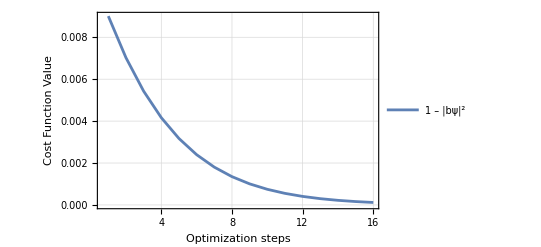

```mathematica
ListPlot[LocalCostFunction@@@NGradientParameters,Joined->True,GridLines->Automatic,PlotRange->All,Frame->True,FrameLabel->{"Optimization steps","Cost Function Value"},PlotLegends->{"1 – |bψ|^2"}]
```

#### Classical Linear System Solving

We can build the A matrix and stateb of the present problem:

A=c_2 A_2+c_3 A_3+c_4 A_4=𝟙+0.2 X_2 Z_3+0.2 X_2

b=U0=H_2 H_3 H_4 0

Solve the system by operating over the corresponding matrices:

```mathematica
A=c[[2]]*IdentityMatrix[8]+
c[[3]]*KroneckerProduct[PauliMatrix[1],PauliMatrix[3],IdentityMatrix[2]]+c[[4]]*KroneckerProduct[PauliMatrix[1],IdentityMatrix[2],IdentityMatrix[2]];
b=ConstantArray[1/Sqrt[8],8];
{"A"->MatrixForm[A],"b"->MatrixForm[b]}
```

{A→(1. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.4 | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0.4 | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0.4 | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.),b→(1/(2 √2)
1/(2 √2)
1/(2 √2)
1/(2 √2)
1/(2 √2)
1/(2 √2)
1/(2 √2)
1/(2 √2))}

Finally, compute the probabilities:

```mathematica
LinearSystemResult=Normalize[LinearSolve[A,b]]^2;
Thread[Delete[0]@#&/@Tuples[{"0","1"},3]->LinearSystemResult]
```

{0,0,0→0.0844595,0,0,1→0.0844595,0,1,0→0.165541,0,1,1→0.165541,1,0,0→0.0844595,1,0,1→0.0844595,1,1,0→0.165541,1,1,1→0.165541}

#### Symbolic & Numeric Quantum Circuit Result

Test the Variational circuit with the optimized parameters results:

```mathematica
VariationalMeasurement=QuantumCircuitOperator[{VariationalBlock,{1,2,3}}][];
```

The symbolic optimization resultant probabilities:

```mathematica
SymbolicResult=VariationalMeasurement[Association[GradientParameters[[2]]]]["Probabilities"]
```

<|000→0.0844595,001→0.0844595,010→0.165541,011→0.165541,100→0.0844595,101→0.0844595,110→0.165541,111→0.165541|>

The numerical optimization resultant probabilities:

```mathematica
NumericalResult=VariationalMeasurement[AssociationThread[{ω1,ω2,ω3},Last@NGradientParameters]]["Probabilities"]
```

<|000→0.0887084,001→0.088708,010→0.161279,011→0.161278,100→0.0887178,101→0.0887174,110→0.161296,111→0.161295|>

We can calculate how different one distribution is from another using the Kullback–Leibler divergence:

```mathematica
Total[#[[1]]*Log[#[[1]]/#[[2]]]&/@Thread[{LinearSystemResult,Values@SymbolicResult}]]
```

-1.72912×10^-16

```mathematica
Total[#[[1]]*Log[#[[1]]/#[[2]]]&/@Thread[{LinearSystemResult,Values@NumericalResult}]]
```

0.000636937

Since the results are small, it is an indicator that the distributions are similar.

We can also employ a Kolmogorov Smirnov Test:

```mathematica
KolmogorovSmirnovTest[Values@SymbolicResult,LinearSystemResult]
```

0.58042

```mathematica
KolmogorovSmirnovTest[Values@NumericalResult,LinearSystemResult]
```

0.282673

In this case, the number is considered big enough to indicate that the results are from the reference distribution.

Let’s plot the probabilities for a visual comparison:

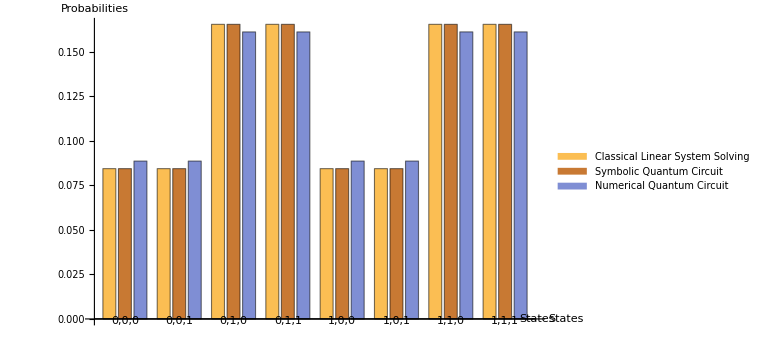

```mathematica
BarChart[Transpose[{LinearSystemResult,Values@SymbolicResult,Values@NumericalResult}],ChartLayout->"Grouped",ChartLabels->{Delete[0]@#&/@Tuples[{"0","1"},3],None},ChartLegends->{"Classical Linear System Solving","Symbolic Quantum Circuit","Numerical Quantum Circuit"},ImageSize->Large,AxesLabel->{"States","Probabilities"}]
```

### QLSP randomly generated

Bravo-Prieto showcase a Randomly generate A matrix:

A=ξ_1(𝟙+ξ_2∑_j ∑_(k ≠j) p a_(j,k)(σ^α)_j(σ^β)_k)

where p follows a binominal distribution, a ϵ (-1,1) and σ are Pauli matrices.

Following the equation, we will consider the following A matrix:

A=1/(8κ)(4(κ+1)𝟙+(κ-1)Z_4+Z_3+2 Z_2)=_(κ->2) (0.75𝟙+0.0625 Z_4+0.0625 Z_3+0.125 Z_2)

and we are given the state:

b=H_2 H_3 H_4 0

Given the ansatz

x=V(ω)0=[R_y(ω_1)⊗R_y(ω_2)⊗R_y(ω_3)]CZ_(2,3)CZ_(2,4)[R_y(ω_4)⊗R_y(ω_5)⊗R_y(ω_6)]CZ_(3,4)CZ_(2,4)[R_y(ω_7)⊗R_y(ω_8)⊗R_y(ω_9)]H_2 H_3 H_4 0

#### Circuit Implementation

Following the same steps, we define the gates associated with the example:

The unitary matrix such that b=U_b 0 :

```mathematica
Ub=QuantumCircuitOperator[{"Hadamard"->{2,3,4}},"Label"->"U_b"];
```

Controlled gates A_l and controlled Z_j :

```mathematica
ControlledGateA=QuantumOperator[QuantumOperator["I"]*KroneckerDelta[l,2]+QuantumOperator[{"CZ"->{1,4}}]*KroneckerDelta[l,3]+QuantumOperator[{"CZ"->{1,3}}]*KroneckerDelta[l,4]+
QuantumOperator[{"CZ"->{1,2}}]*KroneckerDelta[l,5]
,
"Parameters"->{l},
"Label"->"Controlled A_l Gate"];
```

```mathematica
ControlledGateZ=QuantumOperator[
QuantumOperator["CZ"->{1,2}]*KroneckerDelta[j,2]+QuantumOperator["CZ"->{1,3}]*KroneckerDelta[j,3]+QuantumOperator["CZ"->{1,4}]*KroneckerDelta[j,4]+QuantumOperator["I"]*KroneckerDelta[j,-1],
"Parameters"->{j},
"Label"->"Controlled Z_j Gate"
];
```

Ansatz variational circuit:

```mathematica
VariationalBlock=QuantumCircuitOperator[
{"Hadamard"->{1,2,3},
"RY"[ω1]->{1},"RY"[ω2]->{2},"RY"[ω3]->{3},
"CZ"->{1,2},"CZ"->{1,3},
"RY"[ω4]->{1},"RY"[ω5]->{2},"RY"[ω6]->{3},
"CZ"->{2,3},"CZ"->{1,3},
"RY"[ω7]->{1},"RY"[ω8]->{2},"RY"[ω9]->{3}
},
"Label"->"V(ω)","Parameters"->{ω1,ω2,ω3,ω4,ω5,ω6,ω7,ω8,ω9}];
```

In order to obtain μ_(l , l', j) we will implement a circuit that will deploy a Hadamard test:

As the previous example, we implement the Hadamard test:

```mathematica
ClearAll[LocalHadamardCircuit];
LocalHadamardCircuit=QuantumCircuitOperator[{
"Hadamard"->{1},
"P"[θ],
VariationalBlock->{2,3,4},
ControlledGateA,
Ub,
ControlledGateZ,
Ub,
ControlledGateA[<|l->lp|>],
"Hadamard"->{1}
},"Parameters"->{ω1,ω2,ω3,ω4,ω5,ω6,ω7,ω8,ω9,l,lp,j,θ}];
```

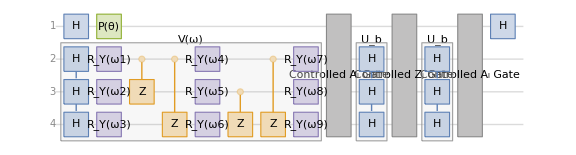

```mathematica
LocalHadamardCircuit["Diagram",ImageSize->Large]
```

#### Local Cost Function

Calculate the symbolic mean value of our function:

```mathematica
LocalHadamardState=LocalHadamardCircuit[];
```

```mathematica
LocalHadamardStateVector=Normal[LocalHadamardState["StateVector"]];
```

Since it can be a heavy computation, we will compute  the state vector variations on the variables that are not part of the Variational Circuit V(ω). Remember that l and l,p correspond to the controlled A_l gates index (from 2 to 5) and j to the qubits (from 2 to 4 and -1 for the normalization term):

```mathematica
LocalHadamardStateVectors=Association@Table[
Rule[{𝕝,𝕝𝕡,𝕛},N@Replace[LocalHadamardStateVector,{l->𝕝,lp->𝕝𝕡,j->𝕛},{7,12}]],
{𝕝,{2,3,4,5}},{𝕝𝕡,{2,3,4,5}},{𝕛,{-1,2,3,4}}];//AbsoluteTiming
```

{14.2163,Null}

Now we will implement the functions to calculate the local cost for this circuit:

```mathematica
H=Normal[QuantumOperator[{"Z"->{1},"I"->{2,3,4}}]["Matrix"]];
```

In this LocalHadamardMeanValues version, we call LocalHadamardStateVectors[{l, lp, j}] for the state vector already computed to save time per each execution of LocalCost:

```mathematica
ClearAll[LocalHadamardMeanValues];
LocalHadamardMeanValues[v1_,v2_,v3_,v4_,v5_,v6_,v7_,v8_,v9_,l_,lp_,j_]:=Module[{ket,bra},
ket=Replace[LocalHadamardStateVectors[{l,lp,j}],Thread[Rule[{ω1,ω2,ω3,ω4,ω5,ω6,ω7,ω8,ω9},{v1,v2,v3,v4,v5,v6,v7,v8,v9}]],{6,23}];
bra=ConjugateTranspose[ket];
bra.H.ket
]
```

Define  μ_(l,v,j) :

```mathematica
ClearAll[μ]
μ[v1_,v2_,v3_,v4_,v5_,v6_,v7_,v8_,v9_,l_,lp_,j_]:=Module[{mu,μRe,μIm},
mu=LocalHadamardMeanValues[v1,v2,v3,v4,v5,v6,v7,v8,v9,l,lp,j];
μRe=Replace[mu,θ->0,{6,7}];
μIm=Replace[mu,θ->-π/2,{6,7}];
N[μRe + j μIm]
]
```

Implement the normalization term:

```mathematica
c={0,0.75,0.0625,0.0625,0.125};
```

```mathematica
ClearAll[PsiNorm];
PsiNorm[w1_?NumericQ,w2_?NumericQ,w3_?NumericQ,w4_?NumericQ,w5_?NumericQ,w6_?NumericQ,w7_?NumericQ,w8_?NumericQ,w9_?NumericQ]:=Abs[
Sum[
c[[l]]*Conjugate[c[[lp]]]*μ[w1,w2,w3,w4,w5,w6,w7,w8,w9,l,lp,-1],
{l,{2,3,4,5}},{lp,{2,3,4,5}}
]
];
```

Following the C_L equation, we define the cost function:

```mathematica
ClearAll[LocalCost];
LocalCost[w1_?NumericQ,w2_?NumericQ,w3_?NumericQ,w4_?NumericQ,w5_?NumericQ,w6_?NumericQ,w7_?NumericQ,w8_?NumericQ,w9_?NumericQ]:=0.5-((0.5/(3*PsiNorm[w1,w2,w3,w4,w5,w6,w7,w8,w9]))*Abs[
Sum[
c[[l]]*Conjugate[c[[lp]]]*μ[w1,w2,w3,w4,w5,w6,w7,w8,w9,l,lp,j],
{l,{2,3,4,5}},{lp,{2,3,4,5}},{j,{2,3,4}}
]
]
);
```

#### Cost Function Optimization

We will calculate the gradient descent for our cost function:

```mathematica
w= 0.001 *RandomVariate[NormalDistribution[],9];
```

```mathematica
GradientParameters=GradientDescent[LocalCost,w,"MaxIterations"->40,"LearningRate"->0.8];//AbsoluteTiming
```

{2286.16,Null}

```mathematica
lc=LocalCost@@@GradientParameters;//AbsoluteTiming
```

{157.964,Null}

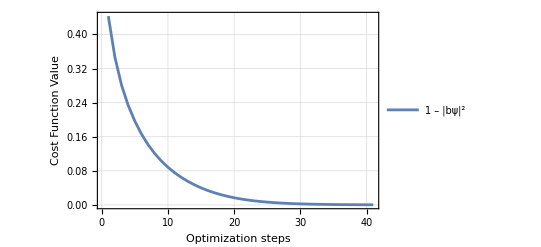

```mathematica
ListPlot[lc,Joined->True,GridLines->Automatic,PlotRange->All,Frame->True,FrameLabel->{"Optimization steps","Cost Function Value"},PlotLegends->{"1 – |bψ|^2"}]
```

#### Classical Linear System Solving

We can build the A matrix and stateb of the present problem:

A= (0.75𝟙+0.0625 Z_4+0.0625 Z_3+0.125 Z_2)

b =H_2 H_3 H_4 0

Solve the system by operating over the correspondent matrices:

```mathematica
A2=IdentityMatrix[8];
A3=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],PauliMatrix[3]];
A4=KroneckerProduct[IdentityMatrix[2],PauliMatrix[3],IdentityMatrix[2]];
A5=KroneckerProduct[PauliMatrix[3],IdentityMatrix[2],IdentityMatrix[2]];
```

```mathematica
A=c[[2]]*A2+c[[3]]*A3+c[[4]]*A4+c[[5]]*A5;
b=ConstantArray[1/Sqrt[8],8];
{"A"->MatrixForm[A],"b"->MatrixForm[b]}//N
```

{A→(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.875 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.875 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.75 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.75 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.625 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.625 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5),b→(0.353553
0.353553
0.353553
0.353553
0.353553
0.353553
0.353553
0.353553)}

Finally, compute the probabilities:

```mathematica
LinearSystemResult=Normalize[LinearSolve[A,b]]^2;
Thread[Delete[0]@#&/@Tuples[{SubPlus[z],SubMinus[z]},3]->LinearSystemResult]
```

{z_+,z_+,z_+→0.0613956,z_+,z_+,z_-→0.0801902,z_+,z_-,z_+→0.0801902,z_+,z_-,z_-→0.109148,z_-,z_+,z_+→0.109148,z_-,z_+,z_-→0.157173,z_-,z_-,z_+→0.157173,z_-,z_-,z_-→0.245583}

#### Symbolic & Numeric Quantum Circuit Result

We can build the Variational circuit from the example and test it with the optimized parameters result:

Test the Variational circuit with the optimized parameters results:

```mathematica
VariationalMeasurement=QuantumCircuitOperator[{VariationalBlock,QuantumMeasurementOperator["Z"->{1,-1},{1,2,3}]}][];
```

The optimization resultant probabilities:

```mathematica
NumericalResult=VariationalMeasurement[AssociationThread[{ω1,ω2,ω3,ω4,ω5,ω6,ω7,ω8,ω9},Last@GradientParameters]]["Probabilities"]
```

<|𝓏_+𝓏_+𝓏_+→0.0621861,𝓏_+𝓏_+𝓏_−→0.0832131,𝓏_+𝓏_−𝓏_+→0.0816941,𝓏_+𝓏_−𝓏_−→0.10831,𝓏_−𝓏_+𝓏_+→0.119605,𝓏_−𝓏_+𝓏_−→0.168693,𝓏_−𝓏_−𝓏_+→0.144291,𝓏_−𝓏_−𝓏_−→0.232007|>

We can calculate how different one distribution is from another using the Kullback–Leibler divergence:

```mathematica
Total[#[[1]]*Log[#[[1]]/#[[2]]]&/@Thread[{LinearSystemResult,Values@NumericalResult}]]
```

0.00189974

Since the results are small, it is an indicator that the distributions are similar.

We can also employ a Kolmogorov Smirnov Test:

```mathematica
KolmogorovSmirnovTest[Values@NumericalResult,LinearSystemResult]
```

0.955245

In this case, the number is considered big enough to indicate that the results are from the reference distribution.

Let’s plot the probabilities for a visual comparison:

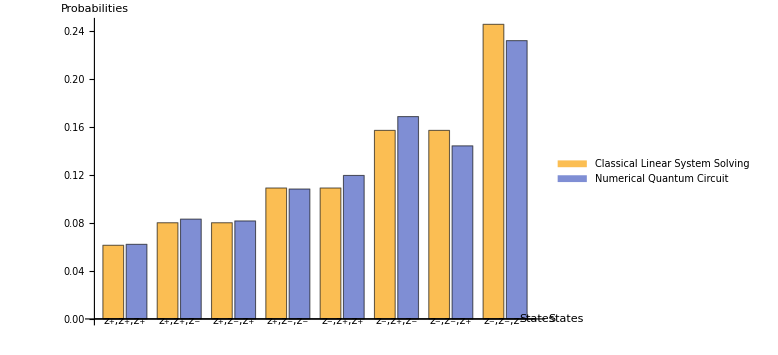

```mathematica
BarChart[Transpose[{LinearSystemResult,Values@NumericalResult}],ChartLayout->"Grouped",ChartLabels->{Delete[0]@#&/@Tuples[{SubPlus[z],SubMinus[z]},3],None},ChartLegends->{"Classical Linear System Solving","Numerical Quantum Circuit"},ImageSize->Large,AxesLabel->{"States","Probabilities"}]
```

## Multiplexer-Based Quantum Linear Solver

### Theory

The Variational Quantum Linear Solver (VQLS) is a a hybrid quantum-classical technique designed to address the Quantum Linear Systems Problem (QLSP). It aims to find linear system solutions using quantum computing techniques.

The classical problem is formulated as follows:

Given a matrix A and vector b, find x such that A.x=b

The corresponding quantum algorithm can be summarized as follows:

Given:

Problem vector: A quantum state b such that b=U0

Problem matrix: 2^n×2^n dimensional matrix A such that A=(∑_0)^(L-1)c_l A_l, where c_l ϵ ℂ  and A_l are unitary gates

We want to prepare:

A quantum state x  such that ψ=Ax  and ψ/(√ψψ)->b

#### Multiplexer-based VQLS

We propose a Multiplexer–Based Variational Quantum Linear Solver (MB-VQLS).  Given a b problem vector and an A problem matrix, the basic steps are:

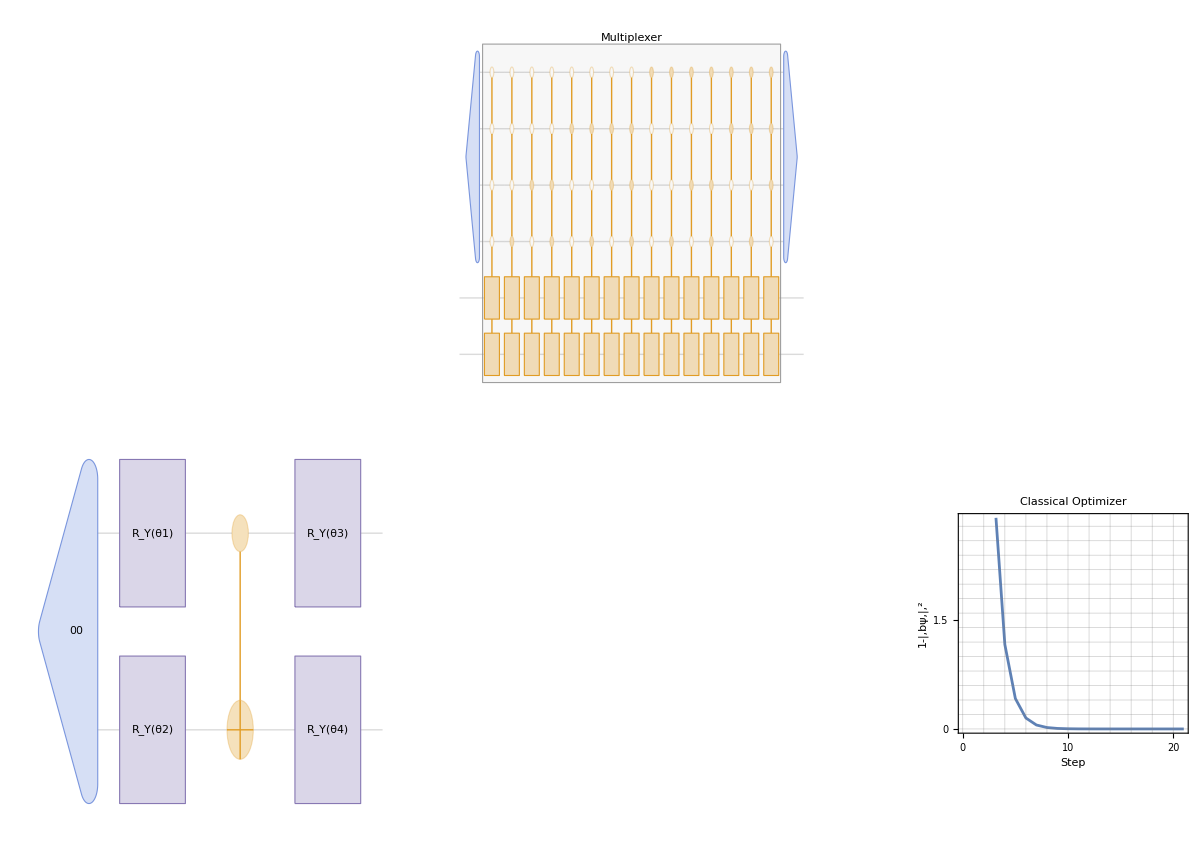

Start with a variational circuit ansatz V(ω_i) or directly an state ansatz x(ω_i)=V(ω_i)0

Apply the multiplexer to perform m.x(ω_i) and obtain resultant ψ(ω_i) state

Use ψ(ω_i) state as the input for the optimizer with the cost function f(ω)=1- |bψ(ω),,|,^2 to obtain new ω_j parameters

Use new ω_j parameters with the variational circuit V(ω_i) or state ansatz x(ω_j)

Repeat the process until you obtain  f(ω_opt)=1- |bψ(ω_opt),,|,^2=0

The primary distinctions between MB–VQLS and a conventional VQLS lie in two key aspects:

The controlled implementation of the matrix A through a multiplexer

Quantum fidelity cost function:

f(ω)=1- |bψ(ω),|,^2

The solution to the linear system is encoded directly in the amplitudes of the resultant quantum state.

Further steps will show that we can avoid some b and A restrictions using their normalization terms. This would help us find solutions for any system.

### A.x Operation Circuit Representation

Considering an n×n A matrix and an n-element vector x, we look to compute the operation A.x with a quantum circuit using A as a controlled operation.

To start, let’s define a complex vector x using RandomComplex, and a random real matrix A called “a”:

```mathematica
x=RandomComplex[{-1-1*I,+1+1*I},4]
```

{-0.126112-0.770322 ⅈ,0.302431-0.0695352 ⅈ,0.0386691-0.00105955 ⅈ,0.0950529-0.0692226 ⅈ}

We will begin the implementation by encoding the matrix A into the quantum circuit:

```mathematica
a=RandomReal[{-1,1},{4,4}];
a//MatrixForm
```

(0.25529 | 0.831537 | 0.774413 | 0.967247
0.345805 | 0.29044 | 0.424374 | -0.428653
-0.406224 | 0.260866 | -0.687513 | 0.829075
-0.901911 | 0.438124 | -0.841926 | -0.108815)

We proceed to generate a quantum operator A and decompose it in Pauli matrices such that A=∑c_j A_j:

```mathematica
A=QuantumOperator[a];
```

```mathematica
pauliDecompose=A["PauliDecompose"]
```

<|XX→0.187644+0. ⅈ,XY→0.+0.426412 ⅈ,XZ→0.0896794+0. ⅈ,XI→0.0944149+0. ⅈ,YX→0.+0.508167 ⅈ,YY→0.154976+0. ⅈ,YZ→0.+0.511854 ⅈ,YI→0.+0.078465 ⅈ,ZX→0.297548+0. ⅈ,ZY→0.-0.296318 ⅈ,ZZ→0.135887+0. ⅈ,ZI→0.335515+0. ⅈ,IX→0.291123+0. ⅈ,IY→0.+0.539183 ⅈ,IZ→-0.153462+0. ⅈ,II→-0.0626495+0. ⅈ|>

In order to implement the controlled A gates, we will turn the Pauli matrices as targets into a multiplexer, and the controlled qubits would be evaluated by a √c state:

```mathematica
multiplexer=QuantumCircuitOperator["Multiplexer"@@Keys[pauliDecompose]];
```

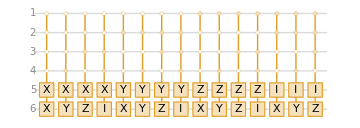

```mathematica
multiplexer["Diagram"]
```

```mathematica
ancillary=QuantumState[Sqrt@Values[pauliDecompose],"Label"->"√c"];
```

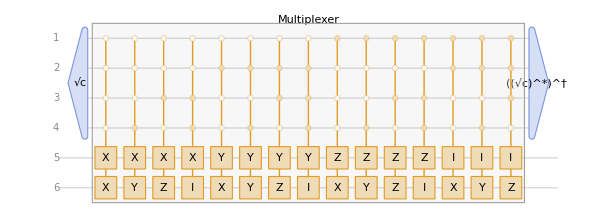

```mathematica
QuantumCircuitOperator[{
ancillary,
multiplexer,
SuperDagger[ancillary["Conjugate"]]
}]["Diagram"]
```

Finally, we would let our vector x be evaluated by the multiplexer in our circuit:

```mathematica
productCircuit=QuantumCircuitOperator[{
ancillary,
QuantumState[x,"Label"->"x"]->{5,6},
multiplexer,
SuperDagger[ancillary["Conjugate"]]
}];
```

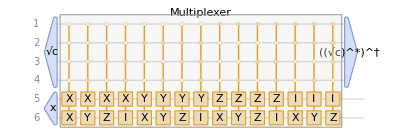

```mathematica
productCircuit["Diagram",ImageSize->Full]
```

Evaluate our circuit and check the amplitudes of the resultant state:

```mathematica
productCircuit[]
```

QuantumState[…]

```mathematica
productCircuit["Table"]
```

| 1
00 | 0.341173-0.322253 ⅈ
01 | 0.0198934-0.257354 ⅈ
10 | 0.182344+0.238122 ⅈ
11 | 0.203345+0.672721 ⅈ

The result corresponds to the equivalent classical operation:

```mathematica
a.x
```

{0.341173-0.322253 ⅈ,0.0198934-0.257354 ⅈ,0.182344+0.238122 ⅈ,0.203345+0.672721 ⅈ}

Now that we learned how to compute the product of a matrix and vector using a quantum circuit, we have a better understanding of how to implement our new variational quantum linear solver.

### Initial problem setup

In order to implement this algorithm, we will start coding a simple example using a random vector b and a random A matrix:

```mathematica
matrixA=RandomReal[{0,1},{4,4}];
```

```mathematica
matrixA//MatrixForm
```

(0.909708 | 0.494552 | 0.49149 | 0.862494
0.724248 | 0.484333 | 0.413379 | 0.721778
0.128352 | 0.905764 | 0.193863 | 0.0352042
0.509416 | 0.602268 | 0.0978288 | 0.510178)

```mathematica
vectorb=RandomReal[{-0.1,+0.1},4]
```

{0.0695503,-0.0689988,0.0678855,0.0997898}

As we previously discussed, we need to save the normalization terms, since we will be working with the normalized matrix and vector:

```mathematica
normA=Norm[matrixA];
normb=Norm[vectorb];
```

In later steps, we will refer to b̂ and Â as the normalized vector b and matrix A, respectively. Then the solution for the Â and b̂ problem would be called x^(^\b)(θ_opt). Applying b and A normalization terms will help us recover the original A.x(θ_opt)=b solution.

### Multiplexer implementation

For this section, we need to repeat what is stated in the A.x Operation Circuit Representation section.

First, we need to decompose Â in Pauli matrices such that Â=∑c_i A_i:

```mathematica
pauliDecompose=QuantumOperator[matrixA/normA]["PauliDecompose"];
```

```mathematica
pauliDecompose
```

<|XX→0.312427+0. ⅈ,XY→0.+0.098157 ⅈ,XZ→-0.081757+0. ⅈ,XI→0.225682+0. ⅈ,YX→0.-0.0161733 ⅈ,YY→-0.00612614+0. ⅈ,YZ→0.+0.0282848 ⅈ,YI→0.+0.0560347 ⅈ,ZX→0.126056+0. ⅈ,ZY→0.-0.0193967 ⅈ,ZZ→0.0861091+0. ⅈ,ZI→0.0801079+0. ⅈ,IX→0.156946+0. ⅈ,IY→0.-0.033938 ⅈ,IZ→0.0126617+0. ⅈ,II→0.243584+0. ⅈ|>

Next, implement the multiplexer:

```mathematica
multiplexer=QuantumCircuitOperator["Multiplexer"@@Keys[pauliDecompose]];
```

```mathematica
ancillary=QuantumState[Sqrt@Values[pauliDecompose],"Label"->"√c"];
```

We obtain the first section of the variational circuit for the VQLS:

```mathematica
qlscircuit=QuantumCircuitOperator[{
ancillary,
multiplexer,
SuperDagger[(ancillary["Conjugate"])]
}];
```

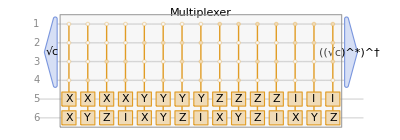

```mathematica
qlscircuit["Diagram",ImageSize->Full]
```

### General symbolic ansatz

Define a general state ansatz for 4-qubits with real amplitudes. Remember we are working with x̂(ω) instead of x(ω); label it so we do not forget about it:

```mathematica
parameters=GenerateParameters[1,4];
ansatz=QuantumState[parameters,"Label"->"x̂(θ)","Parameters"->parameters];
```

```mathematica
ansatz["Formula"]
```

θ100+θ201+θ310+θ411

Finally, we implement the circuit and the correspondent state:

```mathematica
vqlscircuit=qlscircuit[QuantumOperator[ansatz->{5,6}]];
```

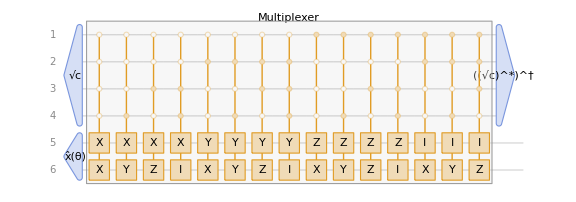

```mathematica
vqlscircuit["Diagram",ImageSize->Large]
```

Wolfram Quantum Framework quantum states (and measurements) keep the parameters defined in previously used circuits, so it would be optimum to work with the resultant state:

```mathematica
ψ=vqlscircuit[]
```

QuantumState[…]

We can perform a first test to obtain ψ(ω_init)=Â.x̂(θ_init):

```mathematica
init=Normalize[0.01*RandomVariate[NormalDistribution[],4]]
```

{0.264994,-0.411396,-0.784879,-0.380126}

```mathematica
ψ[AssociationThread[parameters->init]]["Table"]
```

| 1
00 | -0.313933+0. ⅈ
01 | -0.281493+0. ⅈ
10 | -0.234128+0. ⅈ
11 | -0.178093+0. ⅈ

As we can see, it is not close enough to b̂ in order to call it a good approximation:

```mathematica
QuantumState[vectorb/normb]["Table"]
```

| 1
00 | 0.447414
01 | -0.443866
10 | 0.436705
11 | 0.641944

### Optimization

We are recovering our results from states’ amplitudes and there are some considerations to take into account. The cost function f(θ) we defined previously depends heavily on the quantum fidelity from the b and ψ states:

f(θ)=0↔ℱ=|bψ(θ_opt)|,^2=1

The cost function minimization ensures that the probability distributions of b and ψ are identical, such that:

ψ(θ_opt)=ⅇ^ⅈϕ b

In other words, this cost function does not ensure that the amplitudes of both states are identical, but rather that they are proportional by a global phase:

ψ=∑α_i i &b=∑β_i i ->α_i=ⅇ^ⅈϕ β_i

In order to correct our result, we need to find the global phase and apply it along with the normalization terms for both b and A once our calculation is done, such that:

x_sol=1/ⅇ^ⅈϕ(||b||)/(||A||)x(θ_opt)

Implement the cost functions previously defined, rememer to use the normalized vector b:

```mathematica
qb=QuantumState[vectorb/normb]["Normalize"];
```

```mathematica
fidelity[v1_,v2_,v3_,v4_]:=QuantumDistance[qb,ψ[v1,v2,v3,v4]["Normalize"],"Fidelity"];
```

Now, let’s optimize the cost function using FindMinimum, with our initial guess as the starting point:

```mathematica
ip=Thread[{parameters,init}];
optFM=FindMinimum[fidelity[θ1,θ2,θ3,θ4],ip];//Quiet
```

```mathematica
optFM
```

{0.180515,{θ1→-1.31557×10^10,θ2→-2.58751×10^9,θ3→1.14111×10^10,θ4→8.36485×10^9}}

As we can see, FindMinimum is having some difficulty finding the minimal value, so we might switch to NMinimize, which will return a value for the cost function that is very close to zero:

```mathematica
optNM=NMinimize[fidelity[θ1,θ2,θ3,θ4],{θ1,θ2,θ3,θ4}];
```

```mathematica
optNM
```

{1.42109×10^-14,{θ1→2.73792×10^9,θ2→-6.78883×10^7,θ3→-7.73907×10^8,θ4→-2.33952×10^9}}

Let’s compare the probability distribution of ψ(θ) and b probability distributions:

```mathematica
Dataset[<|"ψ"->ψ[<|Last[optNM]|>]["Probabilities"],"b"->QuantumState[vectorb/normb]["Probabilities"]|>]//Transpose
```

As we can notice, the values are quite close! However, as mentioned earlier, while the probability distributions match, the amplitudes do not necessarily align:

```mathematica
Dataset[<|"ψ"->ψ[<|Last[optNM]|>]["Amplitudes"],"b"->QuantumState[vectorb/normb]["Amplitudes"]|>]//Transpose
```

This is basically is saying that we found ψ(θ_opt)=ⅇ^ⅈϕ b̂:

```mathematica
optψ=ψ[<|Last@optNM|>]["AmplitudesList"]
```

{2.73736×10^7+0. ⅈ,-2.71565×10^7+0. ⅈ,2.67183×10^7+0. ⅈ,3.92752×10^7+0. ⅈ}

The following step is to obtain the global phase ⅇ^ⅈϕ. We can check that it is the same for each amplitude:

```mathematica
globalphase=optψ/(vectorb/normb)
```

{6.11817×10^7+0. ⅈ,6.11817×10^7+0. ⅈ,6.11817×10^7+0. ⅈ,6.11817×10^7+0. ⅈ}

We can verify 1/ⅇ^ⅈϕ ψ(ω_opt)=b̂ using the mean value of the global phase:

```mathematica
1/Mean[globalphase]*optψ-qb["AmplitudesList"]//Chop
```

{-1.26408×10^-7,7.94917×10^-8,6.21723×10^-8,2.04941×10^-7}

Calculate x̂(θ_opt):

```mathematica
optX=ansatz[<|Last@optNM|>]["AmplitudesList"]
```

{2.73792×10^9,-6.78883×10^7,-7.73907×10^8,-2.33952×10^9}

Now recover x(ω_opt) by applying the global phase and normalization terms: x(ω_opt)=1/ⅇ^iϕ(||b||)/(||A||)x̂(ω_opt):

```mathematica
1/Mean[globalphase]*normb/normA*optX//Chop
```

{3.23053,-0.0801031,-0.913152,-2.76045}

We can verify our result:

```mathematica
LinearSolve[matrixA,vectorb]
```

{3.23053,-0.0801031,-0.913152,-2.76045}

```mathematica
%%-%//Abs
```

{6.29597×10^-7,7.79645×10^-8,6.58594×10^-9,6.00327×10^-7}

### Optimization using Quantum Natural Gradient Descent

As explained in a previous example, we can optimize using QuantumNaturalGradientDescent, calculating their correspondent Fubini–Study metric tensor.

A useful question to consider is: “Which state are we using in the Fubini-Study metric tensor function?” In this context, the ansatz does not capture the full geometry of the problem, so the most appropriate choice is the variational state ψ, which is parameterized and encodes the essential information about the system.

```mathematica
fubini=FubiniStudyMetricTensor[ψ];
```

Let’s try with a pair of steps on the optimizer with η->0.6:

```mathematica
opt=GradientDescent[fidelity,init,"LearningRate"->0.6,"MaxIterations"->2];
```

```mathematica
qopt=QuantumNaturalGradientDescent[fidelity,fubini,"InitialPoint"->init,"LearningRate"->0.6,"MaxIterations"->2];
```

The result is quite remarkable: the Quantum Natural Gradient Descent outperforms regular gradient descent and reaches the minimum value in only two steps!

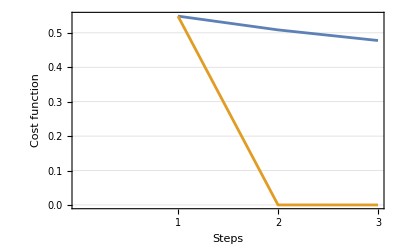

```mathematica
ListLinePlot[{fidelity@@@opt,fidelity@@@qopt},
Frame->True,FrameLabel->{"Steps","Cost function"},
GridLines->Automatic,FrameTicks->{Automatic,{Range[3],None}}]
```

We can verify that the minimization approaches to 0:

```mathematica
fidelity@@@qopt//Last
```

0.0000146428

Checkψ(θ) and b probability distributions:

```mathematica
association=AssociationThread[parameters,Last@qopt];
```

```mathematica
Dataset[<|"ψ"->ψ[association]["Probabilities"],"b"->QuantumState[vectorb/normb]["Probabilities"]|>]//Transpose
```

As you may have noticed, the probabilities match, but with less precision in this case. However, the amplitudes are completely different, and they even have different signs!

```mathematica
Dataset[<|"ψ"->ψ[association]["Amplitudes"],"b"->QuantumState[vectorb/normb]["Amplitudes"]|>]//Transpose
```

This is basically is saying that we found ψ(θ_opt)=ⅇ^ⅈϕ b̂:

```mathematica
optψ=ψ[association]["AmplitudesList"]
```

{-0.516727+0. ⅈ,0.520752+0. ⅈ,-0.505349+0. ⅈ,-0.745124+0. ⅈ}

The following step is to obtain the global phase ⅇ^ⅈϕ:

```mathematica
globalphase=optψ/(vectorb/normb)
```

{-1.15492+0. ⅈ,-1.17322+0. ⅈ,-1.15719+0. ⅈ,-1.16073+0. ⅈ}

Now, during the process of obtaining the global phase, we observe that the values are not exactly the same. In this case, when we use the mean value of the global phase, we can check that the deviation is small enough for the desired precision.

Calculate x(θ_opt):

```mathematica
optX=ansatz[association]["AmplitudesList"]
```

{-52.117+0. ⅈ,1.29782+0. ⅈ,14.7413+0. ⅈ,44.5355+0. ⅈ}

Now recover x(ω_opt) by applying the global phase and normalization terms x(ω_opt)=1/ⅇ^iϕ(||b||)/(||A||)x̂(ω_opt):

```mathematica
1/Mean[globalphase]*normb/normA*optX//Chop
```

{3.23915,-0.0806614,-0.916192,-2.76794}

We can verify our result approximation:

```mathematica
LinearSolve[matrixA,vectorb]
```

{3.23053,-0.0801031,-0.913152,-2.76045}

```mathematica
%%-%//Abs
```

{0.00861713,0.000558259,0.00304054,0.00749401}

After repeating all the same steps from the previous example, we get a final result that is close to the true result but with slightly less precision. What’s remarkable about this solution is that we achieved it in only two steps! Of course, the results depend heavily on the learning rate eta, so it’s important to fine-tune it to ensure that the optimization is done efficiently.